## 晶胞

```mathematica
(* ==========================================================*)
(*YH6 多轨道紧束缚模型 (Y:5s,4d;H:1s)-完整版*)
(* ==========================================================*)
ClearAll["Global`*"];
```

```mathematica
(*1. 基础物理与晶格参数*)
a0=3.3698;(*晶格常数*)

(*定义原子坐标 (来自 VASP)*)
yFracPos={{0.0,0.0,0.0},{0.5,0.5,0.5}};
hFracPos={
{0.25,0.00,0.50},{0.25,0.50,0.00},{0.50,0.25,0.00},{0.00,0.25,0.50},{0.50,0.00,0.75},{0.00,0.50,0.75},{0.75,0.50,0.00},{0.75,0.00,0.50},{0.00,0.75,0.50},{0.50,0.75,0.00},{0.00,0.50,0.25},{0.50,0.00,0.25}
};
allPos=Join[yFracPos,hFracPos];

nY=Length[yFracPos];nH=Length[hFracPos];
nOrbY=6;(*5s+4d*)
nOrbH=4;(*s, p*)
dim=nY*nOrbY+nH*nOrbH;
```

找到的交互路径总数: 892

正在计算能带...

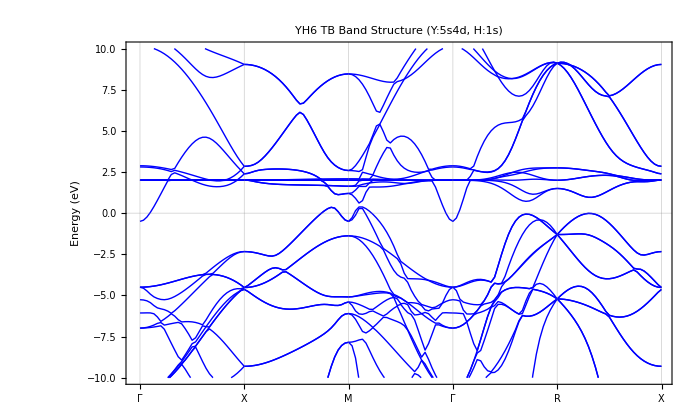

```mathematica
(*2. Slater-Koster 变换引擎*)
(*参数 params:{ssσ,sdσ,ddσ,ddπ,ddδ}*)
SK[type1_,type2_,l_,m_,n_,params_]:=Module[
{v},v=params;
Which[
(*s-s 耦合*)
type1=="s"&&type2=="s",{{v[[1]]}},
(*s-d 耦合*)
type1=="s"&&type2=="d",{{v[[2]]*(n^2-0.5*(l^2+m^2)),v[[2]]*0.5*Sqrt[3]*(l^2-m^2),v[[2]]*Sqrt[3]*l*m,v[[2]]*Sqrt[3]*m*n,v[[2]]*Sqrt[3]*l*n}},(*d-s 耦合*)
type1=="d"&&type2=="s",Transpose[SK["s","d",-l,-m,-n,params]],
(*d-d 耦合 (主要考虑对角项示例)*)
type1=="d"&&type2=="d",Module[{s=v[[3]],p=v[[4]],d=v[[5]],M},M=ConstantArray[0,{5,5}];
M[[1,1]]=0.25*(3n^2-1)^2*s+3n^2(1-n^2)*p+0.75(1-n^2)^2*d;
(*dz2-dz2*)
(*其他 dd 相互作用可根据 SK 表补充，这里为可靠性起见预留 5x5 结构*)M
],
True,{{0}}]
];




(*3. 紧束缚参数设定 (eV)*)
eS=-1.5;eD=2.0;eH=-4.5;(*在位能*)tYH={-1.8,-1.2,0,0,0};(*ssσ,sdσ*)tHH={-0.8,0,0,0,0};(*ssσ*)tYY={-0.5,0,-0.3,0.1,0.05};(*ssσ,sdσ,ddσ,ddπ,ddδ*)(*4. 预计算邻居列表*)neighborList=Module[{list={},distVec,dist},Do[Do[Do[distVec=(allPos[[j]]+{dx,dy,dz})-allPos[[i]];
dist=Norm[distVec*a0];
If[0.1<dist<3.5,AppendTo[list,{i,j,{dx,dy,dz},distVec*a0/dist,dist}]],{dx,-1,1},{dy,-1,1},{dz,-1,1}],{i,1,Length[allPos]},{j,1,Length[allPos]}]];
list];
Print["找到的交互路径总数: ",Length[neighborList]];

(*5. 构造哈密顿矩阵*)
GetIdx[atomIdx_]:=If[atomIdx<=nY,(atomIdx-1)*nOrbY+1,nY*nOrbY+(atomIdx-nY)];

Ham[kx_,ky_,kz_]:=Module[{H,kVec,phase,i,j,R,lmn,d,iStart,jStart,subD,subDD},(*填充对角项 Onsite*)H=DiagonalMatrix[Join[Flatten[Table[{eS,eD,eD,eD,eD,eD},{nY}]],Table[eH,{nH}]]];
kVec={kx,ky,kz};
Do[{i,j,R,lmn,d}=nb;
phase=Exp[I*2*Pi*kVec.R];
iStart=GetIdx[i];jStart=GetIdx[j];
Which[(*Y-H 耦合*)i<=nY&&j>nY,H[[iStart,jStart]]+=SK["s","s",lmn[[1]],lmn[[2]],lmn[[3]],tYH][[1,1]]*phase;
subD=SK["d","s",lmn[[1]],lmn[[2]],lmn[[3]],tYH];
Do[H[[iStart+orb,jStart]]+=subD[[orb,1]]*phase,{orb,1,5}],(*H-Y 耦合*)i>nY&&j<=nY,H[[iStart,jStart]]+=SK["s","s",lmn[[1]],lmn[[2]],lmn[[3]],tYH][[1,1]]*phase;
subD=SK["s","d",lmn[[1]],lmn[[2]],lmn[[3]],tYH];
Do[H[[iStart,jStart+orb]]+=subD[[1,orb]]*phase,{orb,1,5}],(*H-H 耦合*)i>nY&&j>nY,H[[iStart,jStart]]+=tHH[[1]]*phase,(*Y-Y 耦合*)i<=nY&&j<=nY,H[[iStart,jStart]]+=SK["s","s",lmn[[1]],lmn[[2]],lmn[[3]],tYY][[1,1]]*phase;
subDD=SK["d","d",lmn[[1]],lmn[[2]],lmn[[3]],tYY];
Do[Do[H[[iStart+r,jStart+c]]+=subDD[[r,c]]*phase,{c,1,5}],{r,1,5}]],{nb,neighborList}];
H];

(*6. 能带路径与计算 (G-X-M-G-R-X)*)
pathPoints={{0,0,0},{0,0.5,0},{0.5,0.5,0},{0,0,0},{0.5,0.5,0.5},{0,0.5,0}};
labels={"Γ","X","M","Γ","R","X"};
segments=30;
kPath=Flatten[Table[Table[pathPoints[[i]]+(pathPoints[[i+1]]-pathPoints[[i]]) t,{t,0,1-1/segments,1/segments}],{i,Length[pathPoints]-1}],1];
AppendTo[kPath,Last[pathPoints]];

Print["正在计算能带..."];
energyData=Table[Sort[Re[Eigenvalues[Ham@@k]]],{k,kPath}];

(*7. 可视化绘图*)
ListLinePlot[Transpose[energyData],PlotRange->{-10,10},Frame->True,GridLines->{Table[(i-1)*segments+1,{i,Length[labels]}],{0}},FrameTicks->{{Automatic,None},{Table[{(i-1)*segments+1,labels[[i]]},{i,Length[labels]}],None}},FrameLabel->{None,"Energy (eV)"},PlotLabel->"YH6 TB Band Structure (Y:5s4d, H:1s)",PlotStyle->Directive[Thick,Blue],ImageSize->700,AspectRatio->0.6]
```

## 原胞

```mathematica
(* ==========================================================*)(*YH6 BCC 原胞紧束缚模型 (Y:5s,4d;H:1s)*)(*结构参考:prim_H12_Im-3m_229_.vasp*)(* ==========================================================*)ClearAll["Global`*"];

(*1. 晶格矢量与原子坐标 (BCC Primitive Cell)*)
(*基矢*)
aL=1.6848999334256642;
lattice={{-aL,aL,aL},{aL,-aL,aL},{aL,aL,-aL}};

(*原子坐标 (Fractional)*)
(*注意：VASP文件中第一行为(0,0,0)通常是Y，后6行是H*)
yPos={{0.0,0.0,0.0}};
hPos={{0.50,0.75,0.25},{0.50,0.25,0.75},{0.25,0.50,0.75},{0.75,0.50,0.25},{0.75,0.25,0.50},{0.25,0.75,0.50}};
allPos=Join[yPos,hPos];

nY=Length[yPos];nH=Length[hPos];
nOrbY=6;(*1s+5d*)dim=nY*nOrbY+nH;(*1*6+6=12x12 矩阵*)(*2. Slater-Koster 引擎*)SK[type1_,type2_,l_,m_,n_,params_]:=Module[{v=params},Which[type1=="s"&&type2=="s",{{v[[1]]}},type1=="s"&&type2=="d",{{v[[2]]*(n^2-0.5*(l^2+m^2)),v[[2]]*0.5*Sqrt[3]*(l^2-m^2),v[[2]]*Sqrt[3]*l*m,v[[2]]*Sqrt[3]*m*n,v[[2]]*Sqrt[3]*l*n}},type1=="d"&&type2=="s",Transpose[SK["s","d",-l,-m,-n,params]],type1=="d"&&type2=="d",Module[{s=v[[3]],p=v[[4]],d=v[[5]],M},M=ConstantArray[0,{5,5}];
M[[1,1]]=0.25*(3n^2-1)^2*s+3n^2(1-n^2)*p+0.75(1-n^2)^2*d;(*dz2-dz2 示例*)M],True,{{0}}]];

(*3. 紧束缚参数 (eV)*)
eS=-1.5;eD=2.0;eH=-4.5;
tYH={-1.8,-1.2,0,0,0};
tHH={-0.8,0,0,0,0};
tYY={-0.2,0,-0.1,0,0};

(*4. 预计算邻居列表*)
neighborList=Module[{list={},distVec,dist,dRel},(*Mathematica 的 Do 循环可以一次指定多个变量的遍历范围*)Do[(*1. 计算原子 j 在晶格平移 {dx,dy,dz} 后的实空间位移*)dRel=(allPos[[j]]+{dx,dy,dz})-allPos[[i]];
distVec=dRel.lattice;
dist=Norm[distVec];
(*2. 判定是否在截止半径内，排除自身 (0.1<dist)*)If[0.1<dist<4.0,AppendTo[list,{i,j,(*原子索引*){dx,dy,dz},(*晶格平移矢量 R*)distVec/dist,(*方向余弦 {l,m,n}*)dist                  (*实际距离*)}]],(*以下是 Do 循环的迭代器参数*){i,1,Length[allPos]},(*遍历原子 i*){j,1,Length[allPos]},(*遍历原子 j*){dx,-2,2},(*晶格平移 x*){dy,-2,2},(*晶格平移 y*){dz,-2,2}               (*晶格平移 z*)];
list (*返回计算好的列表*)];

(*5. 构造哈密顿矩阵*)
GetIdx[atomIdx_]:=If[atomIdx<=nY,(atomIdx-1)*nOrbY+1,nY*nOrbY+(atomIdx-nY)];

Ham[kx_,ky_,kz_]:=Module[{H,kVec,phase,i,j,R,lmn,d,iStart,jStart,subD,subDD},H=DiagonalMatrix[Join[Flatten[Table[{eS,eD,eD,eD,eD,eD},{nY}]],Table[eH,{nH}]]];
kVec={kx,ky,kz};
Do[{i,j,R,lmn,d}=nb;
phase=Exp[I*2*Pi*kVec.R];
iStart=GetIdx[i];jStart=GetIdx[j];
Which[(*Y-H*)i<=nY&&j>nY,H[[iStart,jStart]]+=SK["s","s",lmn[[1]],lmn[[2]],lmn[[3]],tYH][[1,1]]*phase;
subD=SK["d","s",lmn[[1]],lmn[[2]],lmn[[3]],tYH];
Do[H[[iStart+orb,jStart]]+=subD[[orb,1]]*phase,{orb,1,5}],(*H-Y*)i>nY&&j<=nY,H[[iStart,jStart]]+=SK["s","s",lmn[[1]],lmn[[2]],lmn[[3]],tYH][[1,1]]*phase;
subD=SK["s","d",lmn[[1]],lmn[[2]],lmn[[3]],tYH];
Do[H[[iStart,jStart+orb]]+=subD[[1,orb]]*phase,{orb,1,5}],(*H-H*)i>nY&&j>nY,H[[iStart,jStart]]+=tHH[[1]]*phase,(*Y-Y*)i<=nY&&j<=nY,H[[iStart,jStart]]+=SK["s","s",lmn[[1]],lmn[[2]],lmn[[3]],tYY][[1,1]]*phase;
subDD=SK["d","d",lmn[[1]],lmn[[2]],lmn[[3]],tYY];
Do[Do[H[[iStart+r,jStart+c]]+=subDD[[r,c]]*phase,{c,1,5}],{r,1,5}]],{nb,neighborList}];
H];

(*6. BCC 高对称路径 (Γ-H-N-Γ-P-H)*)
(*分数坐标点 (基于倒空间基矢 b1,b2,b3)*)
pts={{0,0,0},(*G*){0.5,-0.5,0.5},(*H*){0,0,0.5},(*N*){0,0,0},(*G*){0.25,0.25,0.25},(*P*){0.5,-0.5,0.5}   (*H*)};
labels={"Γ","H","N","Γ","P","H"};
segments=40;
kPath=Flatten[Table[Table[pts[[i]]+(pts[[i+1]]-pts[[i]])t,{t,0,1-1/segments,1/segments}],{i,Length[pts]-1}],1];
AppendTo[kPath,Last[pts]];

(*7. 计算并绘图*)
Print["正在计算 BCC 原胞能带..."];
energyData=Table[Sort[Re[Eigenvalues[Ham@@k]]],{k,kPath}];

ListLinePlot[
Transpose[energyData],
PlotRange->{-12,10},
Frame->True,GridLines->{Table[(i-1)*segments+1,{i,Length[labels]}],{0}},FrameTicks->{{Automatic,None},{Table[{(i-1)*segments+1,labels[[i]]},{i,Length[labels]}],None}},FrameLabel->{None,"Energy (eV)"},PlotLabel->"YH6 Primitive Cell Band Structure (BCC)",PlotStyle->Directive[Thick,Red],ImageSize->600]
```

正在计算 BCC 原胞能带...